# Horse shoe prior example

## This example reproducts some results of https://ariddell.org/horseshoe-prior-with-stan.html

### Defines the working directory and loads CmdStan.m

```mathematica
(* Linux *)
SetDirectory["~/GitHub/MathematicaStan/Examples/HorseShoePrior"]

(* Windows *)
(* SetDirectory["C:\\Users\\USER_NAME\\Documents\\Mathematica\\STAN\\Examples\\HorseShoePrior"]; *)

Needs["CmdStan`"]
```

/home/pix/GitHub/MathematicaStan/Examples/HorseShoePrior

### Generates the Horse Shoe Prior Stan code and compiles it

```mathematica
stanCode="data {
  int<lower=0> n;
  int<lower=0> p;
  matrix[n,p] X;
  vector[n] y;
}
parameters {
  vector[p] beta;
  vector<lower=0>[p] lambda;
  real<lower=0> tau;
  real<lower=0> sigma;
}
model {
  lambda ~ cauchy(0, 1);
  tau ~ cauchy(0, 1);
  for (i in 1:p)
    beta[i] ~ normal(0, lambda[i] * tau);
  y ~ normal(X * beta, sigma);
}";
StanCodeExport["horseShoePrior",stanCode]

StanCompile["horseShoePrior"]
```

horseShoePrior.stan

--- Translating Stan model to C++ code ---
bin/stanc /home/pix/GitHub/MathematicaStan/Examples/HorseShoePrior/horseShoePrior.stan --o=/home/pix/GitHub/MathematicaStan/Examples/HorseShoePrior/horseShoePrior.hpp
Model name=horseShoePrior_model
Input file=/home/pix/GitHub/MathematicaStan/Examples/HorseShoePrior/horseShoePrior.stan
Output file=/home/pix/GitHub/MathematicaStan/Examples/HorseShoePrior/horseShoePrior.hpp

--- Linking C++ model ---
g++ -I src -I stan/src -isystem stan/lib/stan_math/ -isystem stan/lib/stan_math/lib/eigen_3.2.8 -isystem stan/lib/stan_math/lib/boost_1.60.0 -isystem stan/lib/stan_math/lib/cvodes_2.8.2/include -Wall -DEIGEN_NO_DEBUG  -DBOOST_RESULT_OF_USE_TR1 -DBOOST_NO_DECLTYPE -DBOOST_DISABLE_ASSERTS -DFUSION_MAX_VECTOR_SIZE=12 -DNO_FPRINTF_OUTPUT -pipe   -lpthread  -O3 -o /home/pix/GitHub/MathematicaStan/Examples/HorseShoePrior/horseShoePrior src/cmdstan/main.cpp -include /home/pix/GitHub/MathematicaStan/Examples/HorseShoePrior/horseShoePrior.hpp stan/lib/stan_math/lib/cvodes_2.8.2/lib/libsundials_nvecserial.a stan/lib/stan_math/lib/cvodes_2.8.2/lib/libsundials_cvodes.a

### Loads data and saves them (RDump file)

```mathematica
yTest=Import["./y-test.dat","List"];
yTrain=Import["./y-train.dat","List"];
XTest= Import["./X-test.dat","Table"];
XTrain= Import["./X-train.dat","Table"];

(* betaLabel is only used for plot legends *)
betaLabel=StringSplit["age sex bmi map tc ldl hdl tch ltg glu age^2 bmi^2 map^2 tc^2 ldl^2 hdl^2 tch^2 ltg^2 glu^2 age:sex age:bmi age:map age:tc age:ldl age:hdl age:tch age:ltg age:glu sex:bmi sex:map sex:tc sex:ldl sex:hdl sex:tch sex:ltg sex:glu bmi:map bmi:tc bmi:ldl bmi:hdl bmi:tch bmi:ltg bmi:glu map:tc map:ldl map:hdl map:tch map:ltg map:glu tc:ldl tc:hdl tc:tch tc:ltg tc:glu ldl:hdl ldl:tch ldl:ltg ldl:glu hdl:tch hdl:ltg hdl:glu tch:ltg tch:glu ltg:glu"," "];

(* Export data *)
RDumpExport["horseShoePrior",{{"n",Dimensions[XTrain][[1]]},{"p",Dimensions[XTrain][[2]]},{"X",XTrain},{"y",yTrain}}];

(* Here we just perform an Ordinary Least Squares to get the residue value *)
betaOLS=LeastSquares[XTrain,yTrain];
Norm[XTest.betaOLS-yTest]^2/Length[yTest]
Norm[Mean[yTrain]-yTest]^2/Length[yTest]
```

0.670749

0.965737

### Runs Stan and gets result

```mathematica
(* use the same seed as the blog post *)
StanSetOptionSample["random seed",5]
```

{{random seed,5}}

```mathematica
(* Run stan *)
StanRunSample["horseShoePrior"]
```

method = sample (Default)
  sample
    num_samples = 1000 (Default)
    num_warmup = 1000 (Default)
    save_warmup = 0 (Default)
    thin = 1 (Default)
    adapt
      engaged = 1 (Default)
      gamma = 0.050000000000000003 (Default)
      delta = 0.80000000000000004 (Default)
      kappa = 0.75 (Default)
      t0 = 10 (Default)
      init_buffer = 75 (Default)
      term_buffer = 50 (Default)
      window = 25 (Default)
    algorithm = hmc (Default)
      hmc
        engine = nuts (Default)
          nuts
            max_depth = 10 (Default)
        metric = diag_e (Default)
        stepsize = 1 (Default)
        stepsize_jitter = 0 (Default)
id = 0 (Default)
data
  file = /home/pix/GitHub/MathematicaStan/Examples/HorseShoePrior/horseShoePrior.data.R
init = 2 (Default)
random
  seed = 5
output
  file = /home/pix/GitHub/MathematicaStan/Examples/HorseShoePrior/output.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)


Gradient evaluation took 0.000134 seconds
1000 transitions using 10 leapfrog steps per transition would take 1.34 seconds.
Adjust your expectations accordingly!


Iteration:    1 / 2000 [  0%]  (Warmup)
Iteration:  100 / 2000 [  5%]  (Warmup)
Iteration:  200 / 2000 [ 10%]  (Warmup)
Iteration:  300 / 2000 [ 15%]  (Warmup)
Iteration:  400 / 2000 [ 20%]  (Warmup)
Iteration:  500 / 2000 [ 25%]  (Warmup)
Iteration:  600 / 2000 [ 30%]  (Warmup)
Iteration:  700 / 2000 [ 35%]  (Warmup)
Iteration:  800 / 2000 [ 40%]  (Warmup)
Iteration:  900 / 2000 [ 45%]  (Warmup)
Iteration: 1000 / 2000 [ 50%]  (Warmup)
Iteration: 1001 / 2000 [ 50%]  (Sampling)
Iteration: 1100 / 2000 [ 55%]  (Sampling)
Iteration: 1200 / 2000 [ 60%]  (Sampling)
Iteration: 1300 / 2000 [ 65%]  (Sampling)
Iteration: 1400 / 2000 [ 70%]  (Sampling)
Iteration: 1500 / 2000 [ 75%]  (Sampling)
Iteration: 1600 / 2000 [ 80%]  (Sampling)
Iteration: 1700 / 2000 [ 85%]  (Sampling)
Iteration: 1800 / 2000 [ 90%]  (Sampling)
Iteration: 1900 / 2000 [ 95%]  (Sampling)
Iteration: 2000 / 2000 [100%]  (Sampling)

 Elapsed Time: 88.1214 seconds (Warm-up)
               28.9074 seconds (Sampling)
               117.029 seconds (Total)

### Uses the results

```mathematica
output=StanImport["output.csv"];
```

Compute beta mean and compare it to OLS solution

```mathematica
beta = Mean[StanVariableColumn["beta", output]];
```

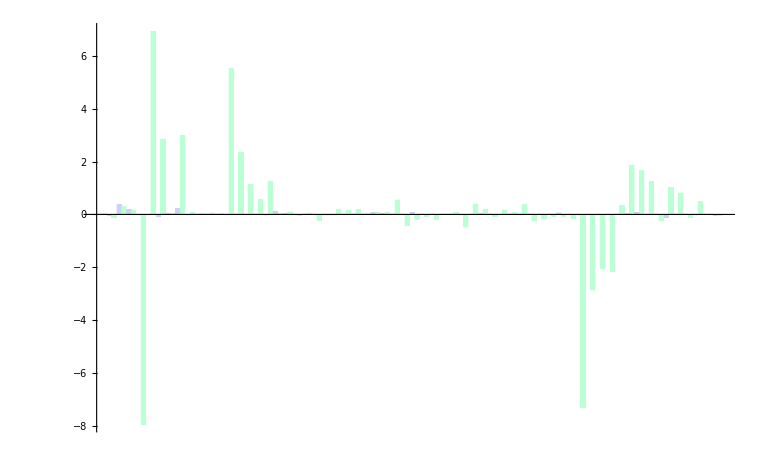
-Graphics--Graphics- | HorseShoe-Graphics- | OLS

```mathematica
BarChart[Transpose[{beta,betaOLS}],ChartLegends->Placed[{"HorseShoe","OLS"},Top]]
```

#### Now selects all beta such that |beta|>0.01

The 21 variables are:
{sex,bmi,map,hdl,tch,ltg,ldl^2,ltg^2,glu^2,age:sex,age:map,age:ltg,sex:bmi,sex:map,sex:hdl,bmi:hdl,map:ltg,ldl:hdl,ldl:tch,hdl:tch,ltg:glu}

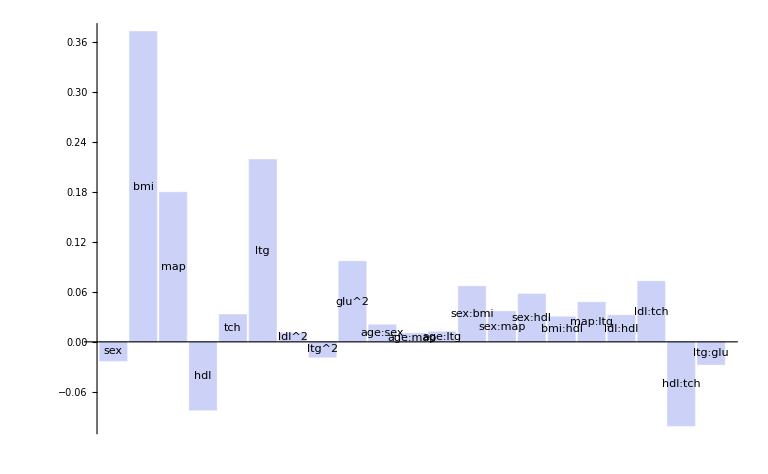

```mathematica
selectedBeta=Map[(Abs[#]>0.01)&,beta];
Print["The ",Count[selectedBeta,True]," variables are:\n",
(betaLabel[[selectedBeta=Flatten[Position[selectedBeta,True]]]])];

selectedBetaLabel=betaLabel[[selectedBeta]];
selectedBeta=beta[[selectedBeta]];

BarChart[selectedBeta,ChartLabels->Placed[selectedBetaLabel,Center]]
```

#### It is interesting to notice that the pruned beta has a better generalization than the OLS solution:

```mathematica
prunedBeta=Map[If[Abs[#]>0.01,#,0]&,beta];
Norm[XTest.betaOLS-yTest]^2/Length[yTest]
Norm[XTest.prunedBeta-yTest]^2/Length[yTest]
```

0.670749

0.50374